# R51 Triplet + C2H2 1st

## MultiWell

## Functions

### Documentation

I am not used to solve master equations by MultiWell, so the function of this script is not comprehensive.

ReadMultiWell[FileName] : Read multiwell *.out file
MultiWellPlot[MultiWellData, ithpT, jthSpecies] : plot <E> and species profile

MultiWellFilt [UNFINISH]: CA, TH
CA: 
There ways:
(1) if product species profile reach its equilavent value and <E> doesn't. k_∞*(prodcut's equilavant value). where k_∞ is the HPL of the CA bimolecular rate constant
(2) if <E> has reached constant, fit  the product species profile where <E> is a constant to A*Exp[k*t], and k_f= A*k_∞  [k_∞*( expolatation value of the product species profile where <E> is a constant to time=0).  More precisly,]
(3) if <E> has reached constant, fit  the product species profile where <E> is a constant to A*Exp[k*t], and k_f= k*Kc, where Kc is the Kc of product and bimolecular reactant 
TH:
One way:
(3) if <E> has reached constant, fit  the product species profile where <E> is a constant to A*Exp[k*t], and k_f= k

### Functions

```mathematica
Clear[TwoAxisListLogandListPlot];
TwoAxisListLogandListPlot[f_List,g_List,opts:OptionsPattern[]]:=Module[{p1,p2,fm,fM,gm,gM,oldgtick,newgtick,newg,oldftick,newftick},p1=ListLogPlot[f,Axes->True,Frame->False,PlotRange->All];
p2=ListPlot[g,Axes->True,Frame->False,PlotRange->{All,{0,Max[g⟦All,2⟧]}}];
{fm,fM}=AbsoluteOptions[p1,PlotRange][[1,2,2]];
{gm,gM}=AbsoluteOptions[p2,PlotRange][[1,2,2]];
oldgtick=AbsoluteOptions[p2,Ticks][[1,2,2]];
newgtick=Flatten[{Rescale[First[#1],{gm,gM},{fm,fM}],Rest[#1]},1]&/@oldgtick;
oldftick=AbsoluteOptions[p1,Ticks][[1,2,2]];
newftick=Flatten[{Exp[First[#1]],Rest[#1]},1]&/@oldftick;
newg={#[[1]],Rescale[#[[2]],{gm,gM},{fm,fM}]}&/@g;
Show[ListPlot[newg,Axes->False,Frame->True,FrameTicks->{Automatic,oldftick,Automatic,newgtick},PlotRange->All,PlotStyle-> Black,opts],
ListLogPlot[{f},Axes->False,Frame->{{True,True},{True,True}},FrameTicks->{Automatic,Automatic,Automatic,newftick},PlotRange->All,PlotStyle-> Blue,opts]]]
```

```mathematica
ReadMultiWell[Name_]:=Module[  (*Read multiwell *.out file*)
{str,iRead,str1,temp,pres,pT,DataArray,Data,label,Databuffer},
DataArray={};
pT={};
str = OpenRead[Name];
iRead = True;
While[iRead,
str1 = Read[str,String];
If[str1== EndOfFile, iRead=False;Break[]];
If[StringCases[str1,"Ttrans"]≠{},
temp=StringReplace[str1,{"     Ttrans = "-> ""," K"-> ""}];
str1 = Read[str,String];
pres = StringReplace[str1,{"     Press  = "-> ""}]//StringTrim;
AppendTo[pT,{temp,pres}];
Data={};
Read[str,String]; Read[str,String]; Read[str,String]; Read[str,String]; Read[str,String]; Read[str,String];
label = Drop[ReadList[StringToStream[Read[str,String]],Word],1];Remove; Read[str,String]; Read[str,String];
str1 = Read[str,String];
While[str1≠ "....................................................",
If[str1== EndOfFile,iRead=False;Break[]];
Databuffer=ReadList[StringToStream[str1],Number];
AppendTo[Data,Databuffer];
str1=Read[str,String];
];
AppendTo[DataArray,Data]
];
]; {pT,label,DataArray}
]
```

```mathematica
MultiWellPlot[MultiWellData_,ithpT_,jthSpecies_]:=Module[  (*plot <E> and species profile*)
{plotframe,plot},
plotframe={{Style["Mole fraction of " <>MultiWellData⟦2,jthSpecies⟧,Italic,17],Style["<Evib> of "<>MultiWellData⟦2,jthSpecies⟧<>" (cm^-1)",Italic,17]},{Style["Time (s). Condition: "<>ToString[MultiWellData⟦1,ithpT⟧],Italic,17],}};
plot=TwoAxisListLogandListPlot[MultiWellData⟦3,ithpT,All,{1,3*jthSpecies}⟧,MultiWellData⟦3,ithpT,All,{1,3*jthSpecies+2}⟧,FrameLabel->plotframe,
                  AspectRatio-> 1/GoldenRatio,
                  PlotMarkers-> {Automatic},
                  Joined-> True,FrameTicksStyle-> 17];
plot//Print
(*species blue, <Evib> black*)
]
```

```mathematica
MultiWellPlotAll[MultiWellData_]:=Module[  (*plot <E> and species profile*)
{plot},
For[i=1,i≤ Length[MultiWellData⟦1⟧],i++,
For[j=1,j≤ Length[MultiWellData⟦2⟧],j++,
plot=MultiWellPlot[MultiWellData,i,j];
plot//Print
];
];
]
```

### Example

```mathematica
MultiWellData=ReadMultiWell["multiwellT1500_0.out"];
```

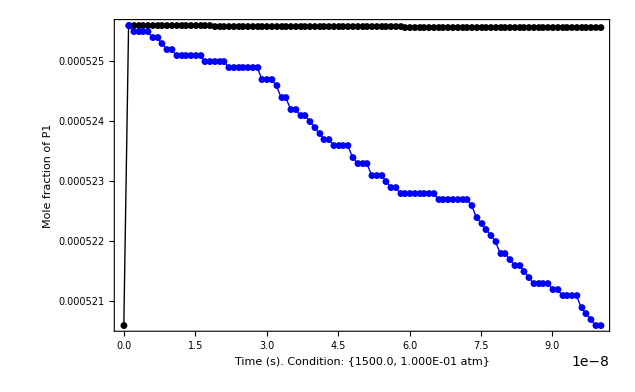

```mathematica
MultiWellPlot[MultiWellData,1,3]
```

```mathematica
MultiWellPlotAll[MultiWellData]
```

## Global Setting

```mathematica
cwd = NotebookDirectory[];
SetDirectory[NotebookDirectory[]]
```

C:\Users\dodo\Desktop\soothair_2nd\2_Systems_FullRev\R51_1st\Results\MultiWell

## pT grid

### at 0.1 atm and 1500 K

```mathematica
MultiWellData=ReadMultiWell["multiwellT1500_0.out"];
```

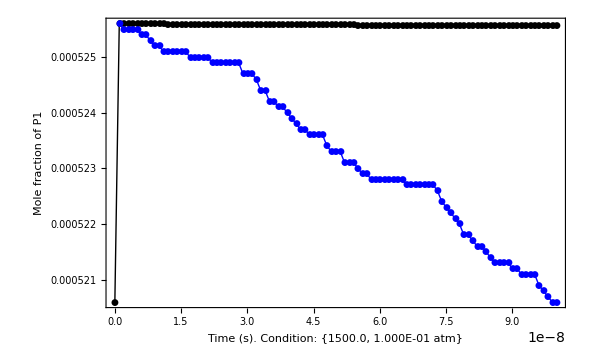

```mathematica
MultiWellPlot[MultiWellData,1,3]
```

Chemical activated: mole fraction of P1 * kinf of reax 1

```mathematica
kinf=2.2111459999999995*^9 cc/mol/s; (*from ctst*)
molfrac=0.00052;
kinf*molfrac
```

(1.1498×10^6 cc)/(mol s)

agree with MESMER's result

### at 1.0 atm and 1500 K

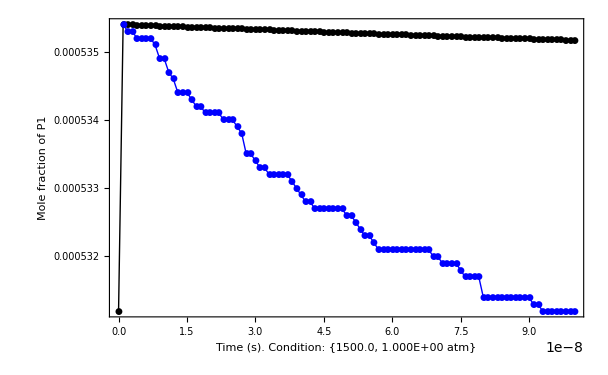

```mathematica
MultiWellPlot[MultiWellData,2,3]
```

Chemical activated: mole fraction of P1 * kinf of reax 1

```mathematica
kinf=2.2111459999999995*^9 cc/mol/s; (*from ctst*)
molfrac=0.00053;
kinf*molfrac
```

(1.17191×10^6 cc)/(mol s)

agree with MESMER's result

### at 10.0 atm and 1500 K

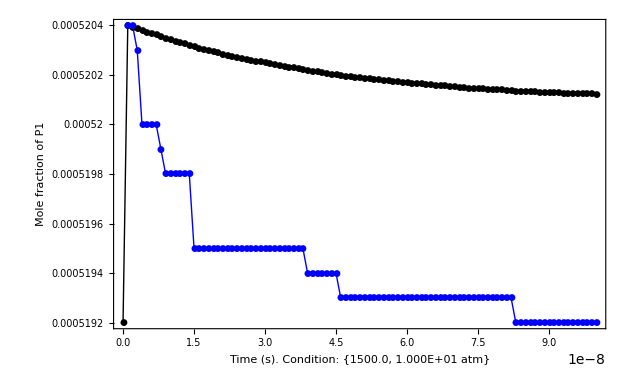

```mathematica
MultiWellPlot[MultiWellData,3,3]
```

### at 0.1 atm and 2000 K

```mathematica
MultiWellData=ReadMultiWell["multiwellT2000_0.out"];
```

```mathematica
MultiWellData⟦1⟧
MultiWellData⟦2⟧
```

{{2000.0,1.000E-01 atm},{2000.0,1.000E+00 atm},{2000.0,1.000E+01 atm}}

{IM1,IM2,P1,R1_R2}

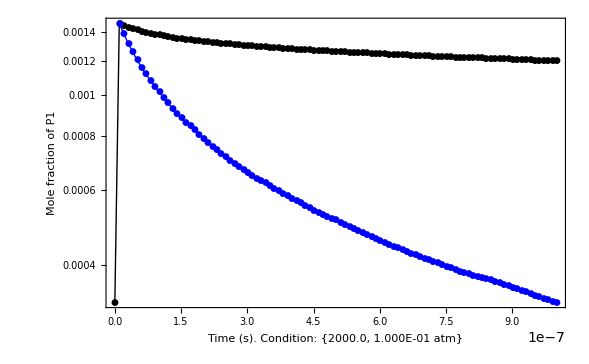

```mathematica
MultiWellPlot[MultiWellData,1,3]
```

Chemical activated: mole fraction of P1 * kinf of reax 1

```mathematica
molfrac=0.00052;
kinf*molfrac
```

(1.1498×10^6 cc)/(mol s)

```mathematica
fitdata=MultiWellData⟦3,1(*0.1atm*),-20;;,{1,9(*P1 profile*)}⟧;
molfrac=FindFit[fitdata,A*ⅇ^(-kf*t),{A,kf},t]⟦1,2⟧;
kinf=2.5073299999999992*^10 cc/mol/s (*from ctst Reax1kf*);
kinf*molfrac
```

(1.81636×10^7 cc)/(mol s)

doesnot agree with MESMER's result (maybe 10^-6s is not long enough, <E> hasn't reach a constant)

### at 1.0 atm and 2000 K

```mathematica
MultiWellData=ReadMultiWell["multiwellT2000_0.out"];
```

```mathematica
MultiWellData⟦1⟧
MultiWellData⟦2⟧
```

{{2000.0,1.000E-01 atm},{2000.0,1.000E+00 atm},{2000.0,1.000E+01 atm}}

{IM1,IM2,P1,R1_R2}

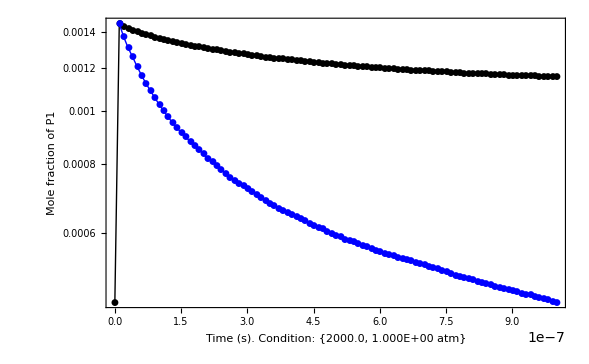

```mathematica
MultiWellPlot[MultiWellData,2,3]
```

Chemical activated: mole fraction of P1 * kinf of reax 1

```mathematica
fitdata=MultiWellData⟦3,2(*1.0atm*),-20;;,{1,9(*P1 profile*)}⟧;
molfrac=FindFit[fitdata,A*ⅇ^(-kf*t),{A,kf},t]⟦1,2⟧;
kinf=2.5073299999999992*^10 cc/mol/s (*from ctst Reax1kf*);
kinf*molfrac
```

(1.8223×10^7 cc)/(mol s)

agree with MESMER's result

### at 10.0 atm and 2000 K

```mathematica
MultiWellData=ReadMultiWell["multiwellT2000_0.out"];
```

```mathematica
MultiWellData⟦1⟧
MultiWellData⟦2⟧
```

{{2000.0,1.000E-01 atm},{2000.0,1.000E+00 atm},{2000.0,1.000E+01 atm}}

{IM1,IM2,P1,R1_R2}

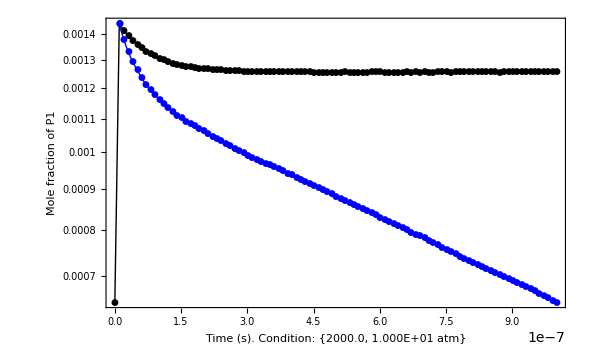

```mathematica
MultiWellPlot[MultiWellData,3,3]
```

Chemical activated: mole fraction of P1 * kinf of reax 1

```mathematica
fitdata=MultiWellData⟦3,3(*10.0atm*),-20;;,{1,9(*P1 profile*)}⟧;
molfrac=FindFit[fitdata,A*ⅇ^(-kf*t),{A,kf},t]⟦1,2⟧;
kinf=2.5073299999999992*^10 cc/mol/s (*from ctst Reax1kf*);
kinf*molfrac
```

(2.96156×10^7 cc)/(mol s)

agree with MESMER's result

```mathematica
fitdata=MultiWellData⟦3,3(*10.0atm*),-20;;,{1,9(*P1 profile*)}⟧;
k=FindFit[fitdata,A*ⅇ^(-kf*t),{A,kf},t]⟦2,2⟧
kc=49.968211507199996(*from Keq overall*);
k*kc
```

595619.

2.9762×10^7